```mathematica
epsilon = 0.05;
```

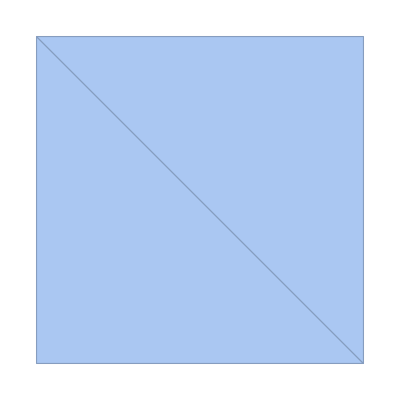

```mathematica
sheet = MeshRegion[{{0,0},{0,1},{1,0},{1,1}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}]
```

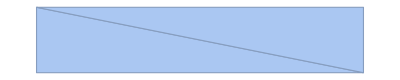

```mathematica
rod = MeshRegion[{{1,0.5-epsilon},{1,0.5+epsilon},{2,0.5-epsilon},{2,0.5+epsilon}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}]
```

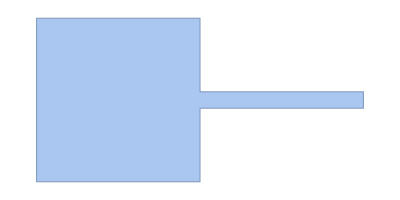

```mathematica
reg = RegionUnion[sheet,rod]
```

```mathematica
Manipulate[Plot3D[{k*x^2*(x-2)^2*y^2*(y-1)^2,3},{x,y}∈reg],{k,0.1,50}]
```

```mathematica
kk = 50;
initFunc[x_,y_]:=kk*x^2*(x-2)^2*y^2*(y-1)^2;
```

```mathematica
(*Whole region, alphaSheet for all diffusion*)
alphaSheet  = 0.02;
diffFunc[x_]:=alphaSheet;
```

```mathematica
regVals = NDSolveValue[{D[u[t,x,y],t]==alphaSheet*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
Manipulate[Plot3D[{regVals[t,x,y],0,3},{x,y}∈reg],{t,0,10}]
```

```mathematica
regVals2 = NDSolveValue[{D[u[t,x,y],t]==diffFunc[x]*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
Manipulate[Plot3D[{regVals2[t,x,y],0,3},{x,y}∈reg],{t,0,10}]
```

```mathematica
alphaRod=0.8;
```

```mathematica
diffFunc2[x_]:=Piecewise[{{alphaSheet,x<1},{alphaRod,x>1}}];
```

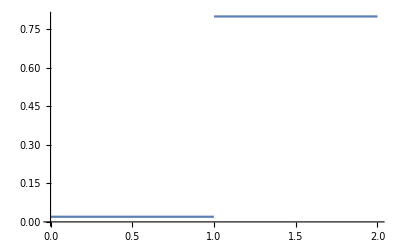

```mathematica
Plot[diffFunc2[x],{x,0,2}]
```

```mathematica
regVals3 = NDSolveValue[{D[u[t,x,y],t]==diffFunc2[x]*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
Manipulate[Plot3D[{regVals3[t,x,y],0,3},{x,y}∈reg],{t,0,10}]
```

```mathematica
Manipulate[Plot3D[{regVals[t,x,y],regVals3[t,x,y],0,3},{x,y}∈reg,PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```

```mathematica
yy=0.5;Manipulate[Plot[{regVals[t,x,yy],regVals3[t,x,yy],0,3},{x,0,2},PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```